### Fernat point ψ=0

```mathematica
y4Sq[x1_,x2_,x3_]:=-(1 + x1^5 + x2^5 + x3^5)^(1/5);
```

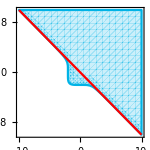

```mathematica
Show[ContourPlot[y4Sq[x1,x2,2]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],ContourStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],RegionPlot[Im[y4Sq[x1,x2,2]]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],PlotStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],ContourPlot[x1==-x2,{x1,-10,10},{x2,-10,10},ContourStyle-> Red]]
```

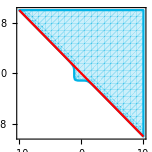

```mathematica
Show[ContourPlot[y4Sq[x1,x2,1]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],ContourStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],RegionPlot[Im[y4Sq[x1,x2,1]]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],PlotStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],ContourPlot[x1==-x2,{x1,-10,10},{x2,-10,10},ContourStyle-> Red]]
```

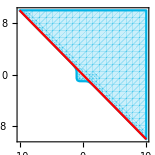

```mathematica
Show[ContourPlot[y4Sq[x1,x2,0]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],ContourStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],RegionPlot[Im[y4Sq[x1,x2,0]]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],PlotStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],ContourPlot[x1==-x2,{x1,-10,10},{x2,-10,10},ContourStyle-> Red]]
```

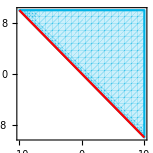

```mathematica
Show[ContourPlot[y4Sq[x1,x2,-1]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],ContourStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],RegionPlot[Im[y4Sq[x1,x2,-1]]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],PlotStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],ContourPlot[x1==-x2,{x1,-10,10},{x2,-10,10},ContourStyle-> Red]]
```

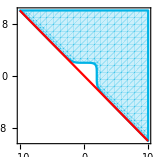

```mathematica
Show[ContourPlot[y4Sq[x1,x2,-2]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],ContourStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],RegionPlot[Im[y4Sq[x1,x2,-2]]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],PlotStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],ContourPlot[x1==-x2,{x1,-10,10},{x2,-10,10},ContourStyle-> Red]]
```

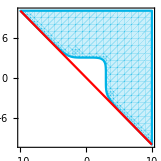

```mathematica
Show[ContourPlot[y4Sq[x1,x2,-3]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],ContourStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],RegionPlot[Im[y4Sq[x1,x2,-3]]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],PlotStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],ContourPlot[x1==-x2,{x1,-10,10},{x2,-10,10},ContourStyle-> Red]]
```

```mathematica
1/5 Re[Integrate[1/(1+u^5+y^5+(z)^5)^(4/5),{y,0,Infinity},{u,0,Infinity},{z,0,Infinity}]]
```

(Gamma[1/5] Gamma[3/10] Gamma[11/10] Gamma[6/5]^2)/(5 2^(1/5) π)

```mathematica
1/5 Im[Integrate[1/(1+u^5+y^5+(z)^5)^(4/5),{y,0,Infinity},{u,0,Infinity},{z,0,Infinity}]]
```

(Gamma[1/5] Gamma[3/10] Gamma[11/10] Gamma[6/5]^2)/(5 2^(1/5) π)

### small ψ

```mathematica
fη[η_,ψ_,u_]:=η^5+1 - 5 ψ u η;
```

```mathematica
FullSimplify[fη[-1,ψ,u]/D[fη[η,ψ,u],η]/.{η->-1}]
```

(u ψ)/(1-u ψ)

```mathematica
FullSimplify[-1 -(u ψ)/(1-u ψ)]
```

1/(-1+u ψ)

```mathematica
Simplify[fη[1/(-1+u ψ),ψ,u]/D[fη[η,ψ,u],η]/.{η->1/(-1+u ψ)}]
```

(1+1/(-1+u ψ)^5-(5 u ψ)/(-1+u ψ))/(-5 u ψ+5/(-1+u ψ)^4)

```mathematica
Simplify[fη[-1-(u ψ)/(1-u ψ),ψ,u]/D[fη[η,ψ,u],η]/.{η->-1-(u ψ)/(1-u ψ)}]
```

(u^2 ψ^2 (10-20 u ψ+15 u^2 ψ^2-4 u^3 ψ^3))/((-1+u ψ)^5 (-5 u ψ+5/(-1+u ψ)^4))

```mathematica
FullSimplify[1/(-1+u ψ)-(u^2 ψ^2 (10-20 u ψ+15 u^2 ψ^2-4 u^3 ψ^3))/((-1+u ψ)^5 (-5 u ψ+5/(-1+u ψ)^4))]
```

(-5+u ψ (5+u ψ (-10+u ψ (10+u ψ (-5+u ψ)))))/(5 (-1+u ψ) (-1+u ψ (-1+u ψ)^4))

```mathematica
y4Sqψ[x1_,x2_,x3_,ψ_]:=-(1 + x1^5 + x2^5 + x3^5)^(1/5) 1/(1 - (x1 x2 x3 ψ)/((1 + x1^5 + x2^5 + x3^5)^(4/5)));
```

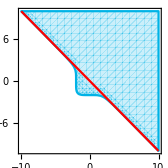

```mathematica
Show[ContourPlot[y4Sqψ[x1,x2,2,0]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],ContourStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],RegionPlot[Im[y4Sqψ[x1,x2,2,0]]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],PlotStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],ContourPlot[x1==-x2,{x1,-10,10},{x2,-10,10},ContourStyle-> Red]]
```

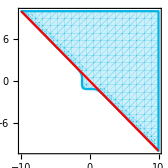

```mathematica
Show[ContourPlot[y4Sqψ[x1,x2,1,0]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],ContourStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],RegionPlot[Im[y4Sqψ[x1,x2,1,0]]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],PlotStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],ContourPlot[x1==-x2,{x1,-10,10},{x2,-10,10},ContourStyle-> Red]]
```

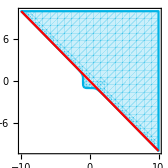

```mathematica
Show[ContourPlot[y4Sqψ[x1,x2,0,0]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],ContourStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],RegionPlot[Im[y4Sqψ[x1,x2,0,0]]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],PlotStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],ContourPlot[x1==-x2,{x1,-10,10},{x2,-10,10},ContourStyle-> Red]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

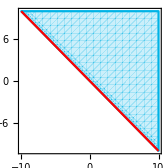

```mathematica
Show[ContourPlot[y4Sqψ[x1,x2,-1,0]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],ContourStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],RegionPlot[Im[y4Sqψ[x1,x2,-1,0]]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],PlotStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],ContourPlot[x1==-x2,{x1,-10,10},{x2,-10,10},ContourStyle-> Red]]
```

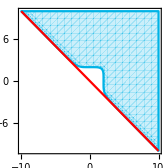

```mathematica
Show[ContourPlot[y4Sqψ[x1,x2,-2,0]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],ContourStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],RegionPlot[Im[y4Sqψ[x1,x2,-2,0]]==0,{x1,-10,10},{x2,-10,10},BoundaryStyle->RGBColor[0,0.7,0.9],PlotStyle->{Opacity[0.2],RGBColor[0,0.7,0.9]},TicksStyle->Directive[FontFamily->"Helvetica", 13,Black]],ContourPlot[x1==-x2,{x1,-10,10},{x2,-10,10},ContourStyle-> Red]]
```

```mathematica
1/5 Re[Integrate[1/(1+u^5+y^5+(z)^5)^(4/5),{y,0,Infinity},{u,0,Infinity},{z,0,Infinity}]]
```

(Gamma[1/5] Gamma[3/10] Gamma[11/10] Gamma[6/5]^2)/(5 2^(1/5) π)

```mathematica
N[%]
```

0.610452

```mathematica
1/5 Im[Integrate[1/(1+u^5+y^5+(z)^5)^(4/5),{y,0,Infinity},{u,0,Infinity},{z,0,Infinity}]]
```

0

O(ψ) - contribution

```mathematica
3/5 Re[Integrate[u y z/(1+u^5+y^5+(z)^5)^(8/5),{y,0,Infinity},{u,0,Infinity},{z,0,Infinity}]]
```

(3 π Gamma[2/5] Gamma[7/5]^2)/(100 2^(2/5) Gamma[9/10] Gamma[13/10])

```mathematica
N[%]
```

0.13005

```mathematica
3/5 Im[Integrate[u y z/(1+u^5+y^5+(z)^5)^(8/5),{y,0,Infinity},{u,0,Infinity},{z,0,Infinity}]]
```

0

O(ψ^2) - contribution

```mathematica
1/5 Integrate[u^2 y^2 z^2/(1+u^5+y^5+(z)^5)^(12/5),{y,0,Infinity},{u,0,Infinity},{z,0,Infinity}]
```

(π Gamma[3/5]^3)/(125 2^(3/5) Gamma[1/10] Gamma[17/10])

```mathematica
N[%]
```

0.00633494

```mathematica
1/5 Im[Integrate[u^2 y^2 z^2/(1+u^5+y^5+(z)^5)^(12/5),{y,0,Infinity},{u,0,Infinity},{z,0,Infinity}]]
```

0

O(ψ^3) - contribution

```mathematica
1/5 Integrate[u^3 y^3 z^3/(1+u^5+y^5+(z)^5)^(16/5),{y,0,Infinity},{u,0,Infinity},{z,0,Infinity}]
```

Gamma[4/5]^4/(625 Gamma[16/5])

```mathematica
N[%]
```

0.00121269

```mathematica
1/5 Im[Integrate[u^3 y^3 z^3/(1+u^5+y^5+(z)^5)^(16/5),{y,0,Infinity},{u,0,Infinity},{z,0,Infinity}]]
```

0

```mathematica
N[((3 π Gamma[2/5] Gamma[7/5]^2)/(100 2^(2/5) Gamma[9/10] Gamma[13/10]))/((Gamma[1/5] Gamma[3/10] Gamma[11/10] Gamma[6/5]^2)/(5 2^(1/5) π))]
```

0.213039

```mathematica
a0=(Gamma[1/5] Gamma[3/10] Gamma[11/10] Gamma[6/5]^2)/(5 2^(1/5) π);
a1=(3 π Gamma[2/5] Gamma[7/5]^2)/(100 2^(2/5) Gamma[9/10] Gamma[13/10]);
a2=(π Gamma[3/5]^3)/(125 2^(3/5) Gamma[1/10] Gamma[17/10]);
```

```mathematica
VolSlag[ψ_,a00_,a10_,a20_]:=a00/a00 - a10/a00 ψ - a20/a00 ψ^2;
```

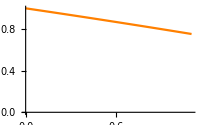

```mathematica
Plot[VolSlag[ψ,a0,a1,a2],{ψ,0,1.1},PlotRange->{0,1},PlotStyle->Orange]
```